# GAA MOSFET Model including source-to-drain Tunneling effect

## title.name

attach file selected

## CONSTANTS INPUT

```mathematica
R = {R1, R1p5, R2, R2p5, R3};
L = {L5, L7, L10};
VBI = {VBI1, VBI2, VBI3, VBI4, VBI5};
VDS = {VDS6, VDS8};
nb1 = NotebookOpen["/home/chengh/DATA/ConstantsINPUT_syn.nb"];
SelectionMove[nb1, All, Notebook];
SelectionEvaluate[nb1];
```

## Function INPUT

```mathematica
nb2=NotebookOpen["/home/chengh/DATA/FunctionINPUT_syn.nb"];
SelectionMove[nb2,All,Notebook];
SelectionEvaluate[nb2];
```

# Calculation Results & Output

## Energy level Results OUTPUT

```mathematica
Plot[{Eq01[VBI[[3]],VGS0,VDS8,zmax[VBI[[3]],VGS0,VDS8,3,1],3,1]/e,Eq01[VBI[[3]],VGS0,VDS8,z,3,1]/e,Eq01[VBI[[3]],VGS2,VDS8,z,3,1]/e,Eq01[VBI[[3]],VGS5,VDS8,z,3,1]/e},{z,0,L[[3]]},PlotRange->{{0,1 L[[3]]},{-.6,.5}},AxesLabel->{z,E01}]
Export["D://My_Data/Mathematica/EXperi/subbandVGS00VDSCONST_Rn_Lm.txt",Table[{z 10^9+9.25,Eq01[VBI[[3]],VGS0,VDS8,z,3,2]/e},{z,0,L[[3]],0.01 L[[3]]}],"CSV"];
Export["D://My_Data/Mathematica/EXperi/subbandVGS02VDSCONST_Rn_Lm.txt",Table[{z 10^9+9.25,Eq01[VBI[[3]],VGS2,VDS8,z,3,2]/e},{z,0,L[[3]],0.01 L[[3]]
}],"CSV"];
Export["D://My_Data/Mathematica/EXperi/subbandVGS05VDSCONST_R_L.txt",Table[{z 10^9+9.5,Eq01[VBI[[3]],VGS5,VDS8,z,3,2]/e},{z,0,L[[3]],0.01 L[[3]]}],"CSV"];
Export["D://My_Data/Mathematica/EXperi/subbandVGSXX_VDS06_RN_L1.txt",Table[{z 10^9+9.5,Eq01[VBI[[2]],VGS0,VDS8,z,2,1]/e,Eq01[VBI[[2]],VGS2,VDS8,z,2,1]/e,Eq01[VBI[[2]],VGS5,VDS8,z,2,1]/e,Eq01[VBI[[3]],VGS0,VDS8,z,3,1]/e,Eq01[VBI[[3]],VGS2,VDS8,z,3,1]/e,Eq01[VBI[[3]],VGS5,VDS8,z,3,1]/e,Eq01[VBI[[4]],VGS0,VDS8,z,4,1]/e,Eq01[VBI[[4]],VGS2,VDS8,z,4,1]/e,Eq01[VBI[[4]],VGS5,VDS8,z,4,1]/e},{z,0,L[[1]],0.01 nm}],"CSV"];
Export["D://My_Data/Mathematica/EXperi/subbandVGSXX_VDS06_RN_L2.txt",Table[{z 10^9+9.5,Eq01[VBI[[2]],VGS0,VDS8,z,2,2]/e,Eq01[VBI[[2]],VGS2,VDS8,z,2,2]/e,Eq01[VBI[[2]],VGS5,VDS8,z,2,2]/e,Eq01[VBI[[3]],VGS0,VDS8,z,3,2]/e,Eq01[VBI[[3]],VGS2,VDS8,z,3,2]/e,Eq01[VBI[[3]],VGS5,VDS8,z,3,2]/e,Eq01[VBI[[4]],VGS0,VDS8,z,4,2]/e,Eq01[VBI[[4]],VGS2,VDS8,z,4,2]/e,Eq01[VBI[[4]],VGS5,VDS8,z,4,2]/e},{z,0,L[[2]],0.01 nm}],"CSV"];
```

Plot::plln: Limiting value L10 in {z,0,L10} is not a machine-sized real number.

Plot[{Eq01[VBI⟦3⟧,VGS0,VDS8,zmax[VBI⟦3⟧,VGS0,VDS8,3,1],3,1]/e,Eq01[VBI⟦3⟧,VGS0,VDS8,z,3,1]/e,Eq01[VBI⟦3⟧,VGS2,VDS8,z,3,1]/e,Eq01[VBI⟦3⟧,VGS5,VDS8,z,3,1]/e},{z,0,L⟦3⟧},PlotRange→{{0,1 L⟦3⟧},{-0.6,0.5}},AxesLabel→{z,E01}]

Export::nodir: Directory /D:/My_Data/Mathematica/EXperi/ does not exist.

OpenWrite::noopen: Cannot open /D://My_Data/Mathematica/EXperi/subbandVGS00VDSCONST_Rn_Lm.txt.

Export::nodir: Directory /D:/My_Data/Mathematica/EXperi/ does not exist.

OpenWrite::noopen: Cannot open /D://My_Data/Mathematica/EXperi/subbandVGS02VDSCONST_Rn_Lm.txt.

Export::nodir: Directory /D:/My_Data/Mathematica/EXperi/ does not exist.

OpenWrite::noopen: Cannot open /D://My_Data/Mathematica/EXperi/subbandVGS05VDSCONST_R_L.txt.

Table::iterb: Iterator {z,0,L5,0.01 nm} does not have appropriate bounds.

Export::nodir: Directory /D:/My_Data/Mathematica/EXperi/ does not exist.

OpenWrite::noopen: Cannot open /D://My_Data/Mathematica/EXperi/subbandVGSXX_VDS06_RN_L1.txt.

Table::iterb: Iterator {z,0,L7,0.01 nm} does not have appropriate bounds.

Export::nodir: Directory /D:/My_Data/Mathematica/EXperi/ does not exist.

OpenWrite::noopen: Cannot open /D://My_Data/Mathematica/EXperi/subbandVGSXX_VDS06_RN_L2.txt.

```mathematica
Eq01[VBI[[3]],VGS0,VDS8,zmax[VBI[[3]],VGS0,VDS8,3,1],3,1]/e
```

Eq01[VBI3,VGS0,VDS8,zmax[VBI3,VGS0,VDS8,3,1],3,1]/e

```mathematica
Plot[{ParabEq01[VBI[[3]],VGS0,VDS8,z,3,1]/e,Eq01[VBI[[3]],VGS0,VDS8,z,3,1]/e,Eq01[VBI[[3]],VGS2,VDS8,z,3,1]/e,ParabEq01[VBI[[3]],VGS2,VDS8,z,3,1]/e},{z,0,L[[3]]},PlotRange->{{0,1 L[[3]]},{-.6,.5}},AxesLabel->{z,E01}]
```

Plot::plln: Limiting value L10 in {z,0,L10} is not a machine-sized real number.

Plot[{ParabEq01[VBI⟦3⟧,VGS0,VDS8,z,3,1]/e,Eq01[VBI⟦3⟧,VGS0,VDS8,z,3,1]/e,Eq01[VBI⟦3⟧,VGS2,VDS8,z,3,1]/e,ParabEq01[VBI⟦3⟧,VGS2,VDS8,z,3,1]/e},{z,0,L⟦3⟧},PlotRange→{{0,1 L⟦3⟧},{-0.6,0.5}},AxesLabel→{z,E01}]

## Energy level Approximation Results OUTPUT

```mathematica
Export["D://My_Data/Mathematica/EXperi/parasubbandVGSXX_VDS06_RN_L1.txt",Table[{z 10^9+9.5,ParabEq01[VBI[[2]],VGS0,VDS8,z,2,1]/e,ParabEq01[VBI[[2]],VGS2,VDS8,z,2,1]/e,ParabEq01[VBI[[2]],VGS5,VDS8,z,2,1]/e,ParabEq01[VBI[[3]],VGS0,VDS8,z,3,1]/e,ParabEq01[VBI[[3]],VGS2,VDS8,z,3,1]/e,ParabEq01[VBI[[3]],VGS5,VDS8,z,3,1]/e,ParabEq01[VBI[[4]],VGS0,VDS8,z,4,1]/e,ParabEq01[VBI[[4]],VGS2,VDS8,z,4,1]/e,ParabEq01[VBI[[4]],VGS5,VDS8,z,4,1]/e},{z,0,L[[1]],0.01 nm}],"CSV"];
Export["D://My_Data/Mathematica/EXperi/parasubbandVGSXX_VDS06_RN_L2.txt",Table[{z 10^9+9.5,ParabEq01[VBI[[2]],VGS0,VDS8,z,2,2]/e,ParabEq01[VBI[[2]],VGS2,VDS8,z,2,2]/e,ParabEq01[VBI[[2]],VGS5,VDS8,z,2,2]/e,ParabEq01[VBI[[3]],VGS0,VDS8,z,3,2]/e,ParabEq01[VBI[[3]],VGS2,VDS8,z,3,2]/e,ParabEq01[VBI[[3]],VGS5,VDS8,z,3,2]/e,ParabEq01[VBI[[4]],VGS0,VDS8,z,4,2]/e,ParabEq01[VBI[[4]],VGS2,VDS8,z,4,2]/e,ParabEq01[VBI[[4]],VGS5,VDS8,z,4,2]/e},{z,0,L[[2]],0.01 nm}],"CSV"];
```

Table::iterb: Iterator {z,0,L5,0.01 nm} does not have appropriate bounds.

Export::nodir: Directory /D:/My_Data/Mathematica/EXperi/ does not exist.

OpenWrite::noopen: Cannot open /D://My_Data/Mathematica/EXperi/parasubbandVGSXX_VDS06_RN_L1.txt.

Table::iterb: Iterator {z,0,L7,0.01 nm} does not have appropriate bounds.

Export::nodir: Directory /D:/My_Data/Mathematica/EXperi/ does not exist.

OpenWrite::noopen: Cannot open /D://My_Data/Mathematica/EXperi/parasubbandVGSXX_VDS06_RN_L2.txt.

## DIBL Results OUTPUT

```mathematica
Plot[{10^6 diblanaids[VBI[[3]],vgs,VDS8,subbandtable,3,2],10^6 anaids[vgs,VDS8,subbandtable,3]},{vgs,0,1},PlotRange->{{0,1 },{-.5,60}},AxesLabel->{Vgs,Ids}]
LogPlot[{diblanaids[VBI[[3]],vgs,VDS8,subbandtable,3,2],anaids[vgs,VDS8,subbandtable,3]},{vgs,0,1},PlotRange->{{0,1 },{10^-14,10^-4}},AxesLabel->{Vgs,Ids}]
Export["D://My_Data/Mathematica/EXperi/DIBLIdsVgs_R_L.txt",Table[{vgs,10^6 diblanaids[VBI[[2]],vgs,VDS8,subbandtable,2,1],10^6 anaids[vgs,VDS8,subbandtable,2],10^6 diblanaids[VBI[[3]],vgs,VDS8,subbandtable,3,1],10^6 anaids[vgs,VDS8,subbandtable,3],10^6 diblanaids[VBI[[4]],vgs,VDS8,subbandtable,4,1],10^6 anaids[vgs,VDS8,subbandtable,4],10^6 diblanaids[VBI[[2]],vgs,VDS8,subbandtable,2,2],10^6 anaids[vgs,VDS8,subbandtable,2],10^6 diblanaids[VBI[[3]],vgs,VDS8,subbandtable,3,2],10^6 anaids[vgs,VDS8,subbandtable,3],10^6 diblanaids[VBI[[4]],vgs,VDS8,subbandtable,4,2],10^6 anaids[vgs,VDS8,subbandtable,4]},{vgs,0,1,0.01}],"CSV"];
Export["D://My_Data/Mathematica/EXperi/IdsVgs_R_L.txt",Table[{vgs,diblanaids[VBI[[2]],vgs,VDS8,subbandtable,2,1],anaids[vgs,VDS8,subbandtable,2],diblanaids[VBI[[3]],vgs,VDS8,subbandtable,3,1],anaids[vgs,VDS8,subbandtable,3],diblanaids[VBI[[4]],vgs,VDS8,subbandtable,4,1], anaids[vgs,VDS8,subbandtable,4],diblanaids[VBI[[2]],vgs,VDS8,subbandtable,2,2],anaids[vgs,VDS8,subbandtable,2],diblanaids[VBI[[3]],vgs,VDS8,subbandtable,3,2],anaids[vgs,VDS8,subbandtable,3],diblanaids[VBI[[4]],vgs,VDS8,subbandtable,4,2], anaids[vgs,VDS8,subbandtable,4]},{vgs,0,1,0.01}],"CSV"];
```

-Graphics-

-Graphics-

Export::nodir: Directory /D:/My_Data/Mathematica/EXperi/ does not exist.

OpenWrite::noopen: Cannot open /D://My_Data/Mathematica/EXperi/DIBLIdsVgs_R_L.txt.

Export::nodir: Directory /D:/My_Data/Mathematica/EXperi/ does not exist.

OpenWrite::noopen: Cannot open /D://My_Data/Mathematica/EXperi/IdsVgs_R_L.txt.

## WKB Transmission Coefficients

```mathematica
Plot[{Numertranscoe[VGS0,VDS8,Ez,3,2],parabolictranscoe[VGS0,VDS8,Ez,3,2],Numertranscoe[VGS1,VDS8,Ez,3,2],parabolictranscoe[VGS1,VDS8,Ez,3,2],Numertranscoe[VGS2,VDS8,Ez,3,2],parabolictranscoe[VGS2,VDS8,Ez,3,2],Numertranscoe[VGS3,VDS8,Ez,3,2],parabolictranscoe[VGS3,VDS8,Ez,3,2],Numertranscoe[VGS4,VDS8,Ez,3,2],parabolictranscoe[VGS4,VDS8,Ez,3,2],Numertranscoe[VGS5,VDS8,Ez,3,2],parabolictranscoe[VGS5,VDS8,Ez,3,2]},{Ez,0,Eq01[VBI[[3]],VGS0,VDS8,zmax[VBI[[3]],VGS0,VDS8,3,2],3,2]},PlotRange->{0,1},AxesLabel->{E01,Transmission Coefficent}]
Export["D://My_Data/Mathematica/EXperi/trans_coe.txt",Table[{Ez/e,parabolictranscoe[VGS0,VDS8,Ez,3,2],parabolictranscoe[VGS1,VDS8,Ez,3,2],parabolictranscoe[VGS2,VDS8,Ez,3,2],parabolictranscoe[VGS3,VDS8,Ez,3,2],parabolictranscoe[VGS4,VDS8,Ez,3,2],parabolictranscoe[VGS5,VDS8,Ez,3,2],Numertranscoe[VGS0,VDS8,Ez,3,2],Numertranscoe[VGS1,VDS8,Ez,3,2],Numertranscoe[VGS2,VDS8,Ez,3,2],Numertranscoe[VGS3,VDS8,Ez,3,2],Numertranscoe[VGS4,VDS8,Ez,3,2],Numertranscoe[VGS5,VDS8,Ez,3,2]},{Ez,0,Eq01[VBI[[3]],VGS0,VDS8,zmax[VBI[[3]],VGS0,VDS8,3,2],3,2],0.01 e}],"CSV"];
```

Plot::plln: Limiting value Eq01[VBI3,VGS0,VDS8,zmax[VBI3,VGS0,VDS8,3,2],3,2] in {Ez,0,Eq01[VBI3,VGS0,VDS8,zmax[VBI3,VGS0,VDS8,3,2],3,2]} is not a machine-sized real number.

Plot[{Numertranscoe[VGS0,VDS8,Ez,3,2],parabolictranscoe[VGS0,VDS8,Ez,3,2],Numertranscoe[VGS1,VDS8,Ez,3,2],parabolictranscoe[VGS1,VDS8,Ez,3,2],Numertranscoe[VGS2,VDS8,Ez,3,2],parabolictranscoe[VGS2,VDS8,Ez,3,2],Numertranscoe[VGS3,VDS8,Ez,3,2],parabolictranscoe[VGS3,VDS8,Ez,3,2],Numertranscoe[VGS4,VDS8,Ez,3,2],parabolictranscoe[VGS4,VDS8,Ez,3,2],Numertranscoe[VGS5,VDS8,Ez,3,2],parabolictranscoe[VGS5,VDS8,Ez,3,2]},{Ez,0,Eq01[VBI⟦3⟧,VGS0,VDS8,zmax[VBI⟦3⟧,VGS0,VDS8,3,2],3,2]},PlotRange→{0,1},AxesLabel→{E01,Transmission Coefficent}]

Table::iterb: Iterator {Ez,0,Eq01[VBI3,VGS0,VDS8,zmax[VBI3,VGS0,VDS8,3,2],3,2],0.01 e} does not have appropriate bounds.

Export::nodir: Directory /D:/My_Data/Mathematica/EXperi/ does not exist.

OpenWrite::noopen: Cannot open /D://My_Data/Mathematica/EXperi/trans_coe.txt.

## Tunneling Current

```mathematica
LogPlot[{numtunnelcurrent[vgs,VDS8,subbandtable,3,2],parabolicapproxtunnelcurrent[vgs,VDS8,subbandtable,4,2]},{vgs,0,1}]
Export["D://My_Data/Mathematica/EXperi/TunnelingIdsVgs_R_L.txt",Table[{vgs,parabolicapproxtunnelcurrent[vgs,VDS8,subbandtable,3,2],numtunnelcurrent[vgs,VDS8,subbandtable,3,2]},{vgs,0,1,0.01}],"CSV"];
```

-Graphics-

Export::nodir: Directory /D:/My_Data/Mathematica/EXperi/ does not exist.

OpenWrite::noopen: Cannot open /D://My_Data/Mathematica/EXperi/TunnelingIdsVgs_R_L.txt.

```mathematica
Export["D://My_Data/Mathematica/EXperi/numTunnelingIdsVgs_R_L.txt",Table[{vgs,numtunnelcurrent[vgs,VDS8,subbandtable,2,1],numtunnelcurrent[vgs,VDS8,subbandtable,3,1],
numtunnelcurrent[vgs,VDS8,subbandtable,4,1],numtunnelcurrent[vgs,VDS8,subbandtable,2,2],numtunnelcurrent[vgs,VDS8,subbandtable,3,2],numtunnelcurrent[vgs,VDS8,subbandtable,4,2]},{vgs,0,1,0.01}],"CSV"];
```

Export::nodir: Directory /D:/My_Data/Mathematica/EXperi/ does not exist.

OpenWrite::noopen: Cannot open /D://My_Data/Mathematica/EXperi/numTunnelingIdsVgs_R_L.txt.

## Total Current

```mathematica
LogPlot[{totalcurrent[vgs,VDS8,subbandtable,2,1],totalcurrent[vgs,VDS8,subbandtable,3,1],totalcurrent[vgs,VDS8,subbandtable,4,1],totalcurrent[vgs,VDS8,subbandtable,2,2],totalcurrent[vgs,VDS8,subbandtable,3,2],totalcurrent[vgs,VDS8,subbandtable,4,2]},{vgs,0,1}]
Export["D://My_Data/Mathematica/EXperi/TotalIdsVgs_R_L.txt",Table[{vgs,totalcurrent[vgs,VDS8,subbandtable,2,1],10^6 totalcurrent[vgs,VDS8,subbandtable,2,1],totalcurrent[vgs,VDS8,subbandtable,3,1],10^6 totalcurrent[vgs,VDS8,subbandtable,3,1],totalcurrent[vgs,VDS8,subbandtable,4,1],10^6 totalcurrent[vgs,VDS8,subbandtable,4,1],totalcurrent[vgs,VDS8,subbandtable,2,2],10^6 totalcurrent[vgs,VDS8,subbandtable,2,2],totalcurrent[vgs,VDS8,subbandtable,3,2],10^6 totalcurrent[vgs,VDS8,subbandtable,3,2],totalcurrent[vgs,VDS8,subbandtable,4,2],10^6 totalcurrent[vgs,VDS8,subbandtable,4,2]},{vgs,0,1,0.01}],"CSV"];
```

-Graphics-

Export::nodir: Directory /D:/My_Data/Mathematica/EXperi/ does not exist.

OpenWrite::noopen: Cannot open /D://My_Data/Mathematica/EXperi/TotalIdsVgs_R_L.txt.

```mathematica
Plot[{totalcurrent[0.45,vds,subbandtable,3,2],totalcurrent[0.55,vds,subbandtable,3,2],totalcurrent[VGS5,vds,subbandtable,3,2],totalcurrent[VGS6,vds,subbandtable,3,2]},{vds,0,1}]
Export["D://My_Data/Mathematica/EXperi/TotalIdsVds_R_L.txt",Table[{vds,totalcurrent[0.45,vds,subbandtable,3,2],totalcurrent[0.55,vds,subbandtable,3,2],totalcurrent[VGS5,vds,subbandtable,3,2],totalcurrent[VGS6,vds,subbandtable,3,2]},{vds,0,1,0.01}],"CSV"];
```

-Graphics-

Export::nodir: Directory /D:/My_Data/Mathematica/EXperi/ does not exist.

OpenWrite::noopen: Cannot open /D://My_Data/Mathematica/EXperi/TotalIdsVds_R_L.txt.

```mathematica
"D:\\OneDrive\\Mathematica\\GAA-MOSFET_proj\\transcoe.txt"
```

D:\OneDrive\Mathematica\GAA-MOSFET_proj\transcoe.txt

# Export

```mathematica
Export["D:\\OneDrive\\Mathematica\\GAA-MOSFET_proj\\deltaug.txt",Table[{vgs,DIBLUG[VBI[[3]],vgs,.5,3,1]},{vgs,0,1,.05}],"CSV"]
Export["D:\\OneDrive\\Mathematica\\GAA-MOSFET_proj\\dibldeltaug.txt",Table[{vgs,Maug[VBI[[3]],vgs,VDS5,2.52 nm,3,1]},{vgs,0,1,.05}],"CSV"]

Export["D:\\OneDrive\\Mathematica\\GAA-MOSFET_proj\\allzmx.txt",Table[{vgs,allzmax[VBI[[3]],vgs,.5,3,1]/nm+9.3},{vgs,0,1,.01}],"CSV"]
Export["D:\\OneDrive\\Mathematica\\GAA-MOSFET_proj\\transcoe0.txt",Table[{(Ez+Eq01[VBI[[3]],0,0.5,0,3,1])/e,allunitranscoe[0,Ez,3,1]},{Ez,-.4 e,e,.02 e}],"CSV"]
Export["D:\\OneDrive\\Mathematica\\GAA-MOSFET_proj\\transcoe1.txt",Table[{(Ez+Eq01[VBI[[3]],0.,0.5,0,3,1])/e,allunitranscoe[0.1,Ez,3,1]},{Ez,-.4 e,e,.02 e}],"CSV"]
Export["D:\\OneDrive\\Mathematica\\GAA-MOSFET_proj\\transcoe2.txt",Table[{(Ez+Eq01[VBI[[3]],0.,0.5,0,3,1])/e,allunitranscoe[0.2,Ez,3,1]},{Ez,-.4 e,e,.02 e}],"CSV"]
Export["D:\\OneDrive\\Mathematica\\GAA-MOSFET_proj\\transcoe3.txt",Table[{(Ez+Eq01[VBI[[3]],0.,0.5,0,3,1])/e,allunitranscoe[0.3,Ez,3,1]},{Ez,-.4 e,e,.02 e}],"CSV"]
Export["D:\\OneDrive\\Mathematica\\GAA-MOSFET_proj\\transcoe4.txt",Table[{(Ez+Eq01[VBI[[3]],0.,0.5,0,3,1])/e,allunitranscoe[0.4,Ez,3,1]},{Ez,-.4 e,e,.02 e}],"CSV"]
Export["D:\\OneDrive\\Mathematica\\GAA-MOSFET_proj\\transcoe5.txt",Table[{(Ez+Eq01[VBI[[3]],0.,0.5,0,3,1])/e,allunitranscoe[0.5,Ez,3,1]},{Ez,-.4 e,e,.02 e}],"CSV"]
Export["D:\\OneDrive\\Mathematica\\GAA-MOSFET_proj\\current.txt",Table[{vgs,e/(Pi hbar)
subbandtable[[1,1]] NIntegrate[Re[allunitranscoe[vgs,Ez,3,1]/(1+Exp[(Eq01[VBI[[3]],vgs,0.5,0,3,1]+Ez)/(kB T)])],{Ez,0,10 e}]},{vgs,0,1,.05}],"CSV"]
```

D:\OneDrive\Mathematica\GAA-MOSFET_proj\deltaug.txt

D:\OneDrive\Mathematica\GAA-MOSFET_proj\dibldeltaug.txt

D:\OneDrive\Mathematica\GAA-MOSFET_proj\allzmx.txt

D:\OneDrive\Mathematica\GAA-MOSFET_proj\transcoe0.txt

D:\OneDrive\Mathematica\GAA-MOSFET_proj\transcoe1.txt

D:\OneDrive\Mathematica\GAA-MOSFET_proj\transcoe2.txt

D:\OneDrive\Mathematica\GAA-MOSFET_proj\transcoe3.txt

D:\OneDrive\Mathematica\GAA-MOSFET_proj\transcoe4.txt

D:\OneDrive\Mathematica\GAA-MOSFET_proj\transcoe5.txt

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ez near {Ez} = {1.10813×10^-20}. NIntegrate obtained 1.03196×10^-21 and 2.23407×10^-27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ez near {Ez} = {1.48261×10^-20}. NIntegrate obtained 6.2602×10^-21 and 1.09621×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ez near {Ez} = {9.36236×10^-21}. NIntegrate obtained 6.90465×10^-21 and 6.86862×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

D:\OneDrive\Mathematica\GAA-MOSFET_proj\current.txt

```mathematica
Table[{vgs,e/(Pi hbar)
subbandtable[[1,1]] NIntegrate[Re[allunitranscoe[vgs,Ez,3,1]/(1+Exp[(Eq01[VBI[[3]],vgs,0.5,0,3,1]+Ez)/(kB T)])],{Ez,0,10 e}]},{vgs,0,1,.05}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ez near {Ez} = {1.10813×10^-20}. NIntegrate obtained 1.03196×10^-21 and 2.23407×10^-27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ez near {Ez} = {1.48261×10^-20}. NIntegrate obtained 6.2602×10^-21 and 1.09621×10^-22 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ez near {Ez} = {9.36236×10^-21}. NIntegrate obtained 6.90465×10^-21 and 6.86862×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{0.,3.01602×10^-10},{0.05,8.4426×10^-10},{0.1,2.46772×10^-9},{0.15,7.49893×10^-9},{0.2,2.35018×10^-8},{0.25,7.50299×10^-8},{0.3,2.39336×10^-7},{0.35,7.36296×10^-7},{0.4,1.99622×10^-6},{0.45,0.0000121097},{0.5,0.0000133563},{0.55,0.0000134367},{0.6,2.33391×10^-7},{0.65,4.89608×10^-8},{0.7,1.56929×10^-8},{0.75,6.52074×10^-9},{0.8,3.02744×10^-9},{0.85,1.63274×10^-9},{0.9,9.45759×10^-10},{0.95,5.97405×10^-10},{1.,4.17526×10^-10}}

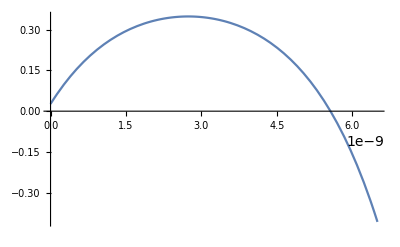

```mathematica
Plot[Eq01[VBI[[3]],0,0.5,z,3,1]/e,{z,0,L[[1]]}]
```

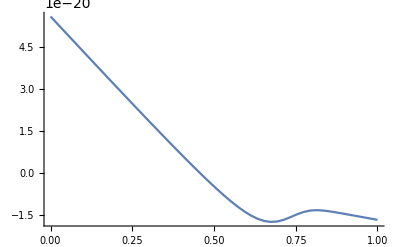

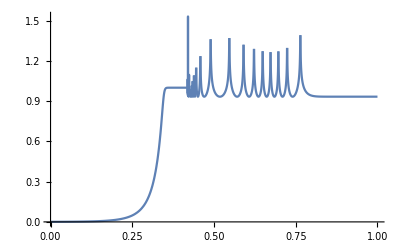

```mathematica
Plot[(Eq01[VBI[[3]],vgs,0.5,allzmax[VBI[[3]],vgs,0.5,3,1],3,1]),{vgs,0,1}]
Plot[Re[allunitranscoe[vgs,.1 e,3,1]],{vgs,0,1}]
```

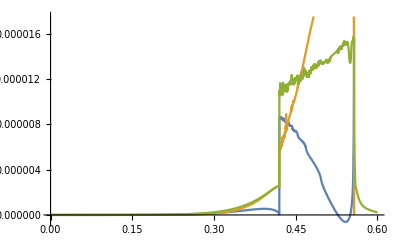

```mathematica
Plot[{e/(Pi hbar)
subbandtable[[1,1]] NIntegrate[Re[allunitranscoe[vgs,Ez,3,1]/(1+Exp[(Eq01[VBI[[3]],vgs,0.5,0,3,1]+Ez)/(kB T)])],{Ez,0,Eq01[VBI[[3]],vgs,0.5,zmax[VBI[[3]],vgs,.5,3,1],3,1]-Eq01[VBI[[3]],vgs,0.5,0,3,1]}],e/(Pi hbar)
subbandtable[[1,1]] NIntegrate[Re[allunitranscoe[vgs,Ez,3,1]/(1+Exp[(Eq01[VBI[[3]],vgs,0.5,0,3,1]+Ez)/(kB T)])],{Ez,Eq01[VBI[[3]],vgs,0.5,zmax[VBI[[3]],vgs,0.5,3,1],3,1],10 e}],e/(Pi hbar)
subbandtable[[1,1]] NIntegrate[Re[allunitranscoe[vgs,Ez,3,1]/(1+Exp[(Eq01[VBI[[3]],vgs,0.5,0,3,1]+Ez)/(kB T)])],{Ez,0,10 e}]},{vgs,0,.6}]
```

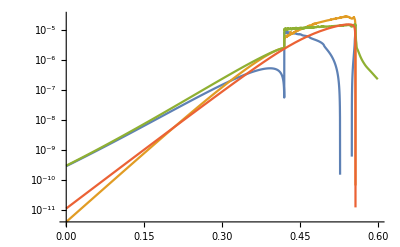

```mathematica
LogPlot[{e/(Pi hbar)
subbandtable[[1,1]] NIntegrate[Re[allunitranscoe[vgs,Ez,3,1]/(1+Exp[(Eq01[VBI[[3]],vgs,0.5,0,3,1]+Ez)/(kB T)])],{Ez,0,Eq01[VBI[[3]],vgs,0.5,zmax[VBI[[3]],vgs,.5,3,1],3,1]-Eq01[VBI[[3]],vgs,0.5,0,3,1]}],e/(Pi hbar)
subbandtable[[1,1]] NIntegrate[Re[allunitranscoe[vgs,Ez,3,1]/(1+Exp[(Eq01[VBI[[3]],vgs,0.5,0,3,1]+Ez)/(kB T)])],{Ez,Eq01[VBI[[3]],vgs,0.5,zmax[VBI[[3]],vgs,0.5,3,1],3,1],10 e}],e/(Pi hbar)
subbandtable[[1,1]] NIntegrate[Re[allunitranscoe[vgs,Ez,3,1]/(1+Exp[(Eq01[VBI[[3]],vgs,0.5,0,3,1]+Ez)/(kB T)])],{Ez,0,10 e}],(e kB T)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[-Eq01[VBI[[3]],vgs,0.5,zmax[VBI[[3]],vgs,0.5,3,1],3,1]/(kB T)]])},{vgs,0,.6}]
```

```mathematica
FindRoot[Eq01[VBI[[3]],vgs,0.5,0,3,1]==Eq01[VBI[[3]],vgs,0.5,zmax[VBI[[3]],vgs,0.5,3,1],3,1],{vgs,0.4}]
```

{vgs→0.527429}

```mathematica
Export["D:\\OneDrive\\Mathematica\\GAA-MOSFET_proj\\inverscurrent.txt",Table[{vgs,Re[(e kB T)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[-Eq01[VBI[[3]],vgs,0.5,zmax[VBI[[3]],vgs,0.5,3,1],3,1]/(kB T)]])]},{vgs,0,.6,.05}],"CSV"]
Export["D:\\OneDrive\\Mathematica\\GAA-MOSFET_proj\\subthcurrent.txt",Table[{vgs,Re[e/(Pi hbar)
subbandtable[[1,1]] NIntegrate[Re[allunitranscoe[vgs,Ez,3,1]/(1+Exp[(Eq01[VBI[[3]],vgs,0.5,0,3,1]+Ez)/(kB T)])],{Ez,0,Eq01[VBI[[3]],vgs,0.5,zmax[VBI[[3]],vgs,.5,3,1],3,1]-Eq01[VBI[[3]],vgs,0.5,0,3,1]}]]},{vgs,0,.6,.05}],"CSV"]
```

D:\OneDrive\Mathematica\GAA-MOSFET_proj\inverscurrent.txt

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ez near {Ez} = {2.40763×10^-21}. NIntegrate obtained 3.79198×10^-21 and 3.00372×10^-25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ez near {Ez} = {6.19831×10^-22}. NIntegrate obtained 1.42533×10^-21 and 8.78606×10^-27 for the integral and error estimates.

D:\OneDrive\Mathematica\GAA-MOSFET_proj\subthcurrent.txt

```mathematica
Table[{vgs,Re[(e kB T)/(Pi hbar) subbandtable[[1,1]] (Log[(1+Exp[-Eq01[VBI[[3]],vgs,0.5,zmax[VBI[[3]],vgs,0.5,3,1],3,1]/(kB T)])/(1+Exp[-Eq01[VBI[[3]],vgs,0.5,zmax[VBI[[3]],vgs,0.5,3,1],3,1]/(kB T)-.5/vt])])]},{vgs,0,.6,.05}]
```

{{0.,1.11729×10^-11},{0.05,5.07171×10^-11},{0.1,2.29354×10^-10},{0.15,1.03222×10^-9},{0.2,4.61604×10^-9},{0.25,2.04569×10^-8},{0.3,8.93258×10^-8},{0.35,3.78278×10^-7},{0.4,1.48099×10^-6},{0.45,4.76943×10^-6},{0.5,0.0000109748},{0.55,0.0000154347},{0.6,0.0000297248}}